## Some quatities

Hubble distance

```mathematica
Subscript[H, 0]=71 km/s  MPc^-1 =
```

```mathematica
71*10^3/(3*10^8)
```

71/300000

## LCDM

```mathematica
kLCDM[a_]:=71/300000/NIntegrate[1/(√(0.734 x^4+8.09 *10^-5+0.26463 x)),{x,0,a}];
GrowLCDM[a_] :=1/(0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,a}]) 0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,1}];
ListPlot[Table[{kLCDM[a],GrowLCDM[a]},{a,0.0000001,1.01,0.01}],Joined->True, AxesLabel-> {k,SubPlus[D]},AxesOrigin -> {0,0.2}]
ParametricPlot[{kLCDM[a],GrowLCDM[a]},{a,0,1}]
GrowfitLCDM[x_]=Fit[Table[{kLCDM[a],GrowLCDM[a]},{a,0.01,1,0.01}], {1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
GrowfitLCDM[1]
ListPlot[{Table[{kLCDM[x],GrowfitLCDM[x]},{x,0.01,1,0.01}],Table[{kLCDM[x],GrowLCDM[x]},{x,0.01,1,0.01}]}]
ListPlot[Table[{x,GrowfitLCDM[x]},{x,0.01,1,0.01}]]
```

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.721646}. NIntegrate obtained -2.43123 + 4.02693\ ⅈ and 0.412471 for the integral and error estimates.

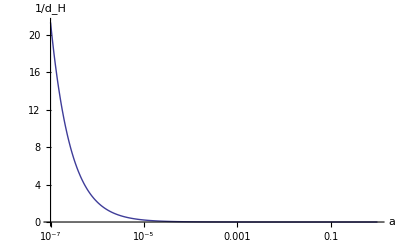

NIntegrate::nlim: m = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {-0.719472}. NIntegrate obtained 2959.38  + 48.2959\ ⅈ
 and 2904.69 for the integral and error estimates.

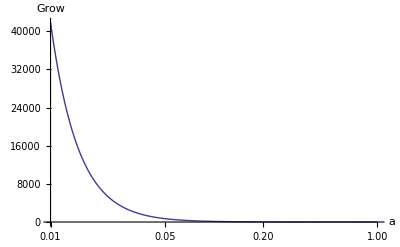

-Graphics-

```mathematica
kLCDM[a_]:=71/300000/NIntegrate[1/(√(0.734 x^4+8.09 *10^-5+0.26463 x)),{x,0,a}];
GrowLCDM[a_] :=1/(0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,a}]) 0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,1}];
LogLinearPlot[kLCDM[a],{a,10^-7,1},AxesLabel-> {a,1/Subscript[d, H]},AxesOrigin-> {10^-7,0},PlotRange->Full,WorkingPrecision->MachinePrecision]
LogLinearPlot[GrowLCDM[a],{a,0.01,1},AxesLabel-> {a,Grow},AxesOrigin-> {0.01,0},PlotRange->Full,WorkingPrecision->MachinePrecision]
ParametricPlot[{kLCDM[a],GrowLCDM[a]},{a,10^-7,1},AspectRatio->1/10]
```

## sCDM

```mathematica
ksCDM[a_]:=1/NIntegrate[1/(√(0.0000809+0.9999191 x)),{x,0,a}];
GrowsCDM[a_] := 1/(2.5NIntegrate[1/((0.0000809/m^4+0.9999191/m^3)^1.5 m^3),{m,0,a}])2.5NIntegrate[1/((0.0000809/m^4+0.9999191/m^3)^1.5 m^3),{m,0,1}];
```

## Draft

```mathematica
kLCDM[a_]:=1/NIntegrate[1/(√(0.734 x^4+8.09 *10^-5+0.26463 x)),{x,0,a}];
GrowLCDM[a_] :=0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,a,1}];
ListPlot[Table[{kLCDM[a],GrowLCDM[a]},{a,0.001,1,0.001}],Joined->True, AxesLabel-> {k,SubPlus[D]},AxesOrigin -> {0,0.2}]
GrowfitLCDM[x_]=Fit[Table[{kLCDM[a],GrowLCDM[a]},{a,0.01,1,0.01}], {1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
GrowfitLCDM[1]
ListPlot[{Table[{x,GrowfitLCDM[x]},{x,0.01,1,0.01}],Table[{k[x],GrowLCDM[x]},{x,0.01,1,0.01}]}]
ListPlot[Table[{x,GrowfitLCDM[x]},{x,0.01,1,0.01}]]
```

```mathematica
LogLinearPlot[(71/300000)/NIntegrate[1/(√(0.734 x^4+8.09 *10^-5+0.26463 x)),{x,0,a}],{a,0.00000001,1}]
Plot[1/(0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,a}]) 0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,1}],{a,0,1}]
ParametricPlot[{(71/300000)/NIntegrate[1/(√(0.734 x^4+8.09 *10^-5+0.26463 x)),{x,0,a}],1/(0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,a}]) 0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,1}]},{a,0.000001,1}]
```